# Hamiltonian

Description
We write the Hamiltonia matrix of one Sz-subspace.
The Hamiltonian is created using the site-basis.
The eigenvalues and eigenstates of the matrix are computed.

.9f Notation
*) chainsize = number of sites
*) upspins = number of spins pointing up in the z direction
*) dim = dimension of the subspace being studied =(chainsize
upspins)  
*) Jxy = strength of the flip-flop term between nearest neighbors
*) Jz = strength of the Ising interaction between nearest neighbors
*) basis = all possible configurations of up and down spins in the given subspace. These create the site-basis of the subspace.
They are obtained by permutation of the state where the first sites have spins pointing up and the others have spins pointing down.
*) HH = elements of the Hamiltonian
*) Energy = eigenvalues of the Hamiltonian
*) Vector = eigenstates of the Hamiltonian
*) open = determines whether the chain is open or closed. For closed chain, open=0. For open chain, open=1

## Code for eigenvalues and eigenstates

```mathematica
(*Parameters of the Hamiltonian*)
Clear[chainsize,upspins,downspins,dim,Jxy,Jz,open];
chainsize=10;
upspins=chainsize/2;
downspins=chainsize-upspins;
dim=chainsize!/(upspins!downspins!);
Jxy=1.0;
Jz=10;
open=1;
(*Creating the basis*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(*ELEMENTS OF THE HAMILTONIAN*)
(*Initialization*)
Clear[HH];
Do[Do[HH[i,j]=0.,{j,1,dim}],{i,1,dim}];

(*Diagonal elements-Ising interaction*)
Do[
Do[
HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,k]]+basis[[i,k+1]]);
       ,{k,1,chainsize-1}];
,{i,1,dim}];
(*Term included in the Ising interaction if the chain is closed*)
If[open==0,
Do[HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,chainsize]]+basis[[i,1]]),
{i,1,dim}]];

(*Off-diagonal elements-flip-flop term*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0
Do[site[z]=0,{z,1,chainsize}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]≠basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];,{k,1,chainsize}];
(*Coupling matrix element-when only two neighbor sites differ*)
If[howmany==2,If[site[2]-site[1]==1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
(*Additional term for closed system*)
If[open==0, If[site[2]-site[1]==chainsize-1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
,{j,i+1,dim}];
,{i,1,dim-1}];

(* TOTAL HAMILTONIAN AND DIAGONALIZATION *)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];
```

# Histogram

.9f Description
We make histograms for the diagonal elements of the Hamiltonian and for its eigenvalues.
The histograms provide us with information on what to expect for the dynamics of the given system.
The choice of the bin width is arbitrary.
Histogram for diagonal elments: a very small value is a good choice, or instead one can use the analytical
expressions provided in the paper.
Histogram for the eigenvalues: have a look at the minimum and maximum values of the eigenvalues before deciding a good value.
NOTE: Mathematica has a command to make histograms, but we found it better to create our own procedure.
(The code provided here is used to obtain the top of Figure 1 in the paper).

.9f Notation
*) binsize = width of each bin
*) binedge = the extremes of the bin
*) Nofbins = number of bins
*) Num = how many states contribute to the height of each bin

## Code for Histogram Histogram of the diagonal elements of the Hamiltonia

```mathematica
(*List of diagonal elements*)
Clear[diagE];
diagE=Sort[Table[HH[i,i],{i,1,dim}]];
(*Parameters for the histogram*)
Clear[binsize,minDiagE,maxDiagE,Nofbins];
binsize=0.01;
minDiagE=Min[diagE];
maxDiagE=Max[diagE];
Nofbins=Floor[(maxDiagE-minDiagE)/binsize]+1;
Clear[binedge];
binedge[1]=minDiagE;
Do[binedge[k]=binedge[k-1]+binsize,{k,2,Nofbins+1}];

(*Number of states in each bin*)
Clear[Num];
Do[Num[k]=0,{k,1,Nofbins}];
Do[Do[If[binedge[k]≤HH[j,j]<binedge[k+1],Num[k]=Num[k]+1];
,{k,1,Nofbins}];
,{j,1,dim}];
```

# .9f Plot of the histogram of the diagonal elements of the Hamiltonian

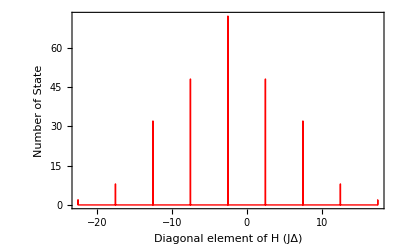

```mathematica
(*Histogram*)
Clear[histData];
histData={{binedge[1],0}};
Do[
histData=Append[histData,{binedge[k],Num[k]}];
histData=Append[histData,{binedge[k+1],Num[k]}];
,{k,1,Nofbins}];
histData=Append[histData,{binedge[Nofbins+1],0}];
ListPlot[histData,Joined->True, LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{{"Number of State",""},{" Diagonal element of H (JΔ)","Diagonal element(Δ=10)"}},Filling->Axis]
```

# Code for Histogram Histogram of the eigenvalues

```mathematica
(*Parameters for the histogram*)
Clear[binsize,minE,maxE,Nofbins];
binsize=0.2;
minE=Floor[Min[Energy]];
maxE=Floor[Max[Energy]]+1;
Nofbins=IntegerPart[(maxE-minE)/binsize];
Clear[binedge];
binedge[1]=minE;
Do[binedge[k]=binedge[k-1]+binsize,{k,2,Nofbins+1}];
(*Number of states in each bin*)
Clear[Num];
Do[Num[k]=0,{k,1,Nofbins}];
Do[
Do[If[binedge[k]≤Energy[[j]]<binedge[k+1],Num[k]=Num[k]+1];
,{k,1,Nofbins}];
,{j,1,dim}];
```

# .9f Plot of the histogram of the eigenvalues

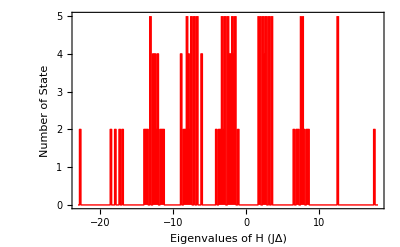

```mathematica
(*Histogram*)
Clear[histData];
histData={{binedge[1],0}};
Do[
histData=Append[histData,{binedge[k],Num[k]}];
histData=Append[histData,{binedge[k+1],Num[k]}];
,{k,1,Nofbins}];
histData=Append[histData,{binedge[Nofbins+1],0}];
ListPlot[histData,Joined->True, LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{{"Number of State",""},{" Eigenvalues of H (JΔ)","Eigenvalues(Δ=10)"}},Filling->Axis, FillingStyle->Red]
```